Corso di Laboratorio Computazionale, Corso di Laurea in Matematica,  Università di Padova.        
A.A. 2021-2022

# Esercizi 1: Grafica e numeri primi

Notebook del gruppo:  Pinguini tattici nucleari

Componenti del gruppo: Nicole Mietto e Lorena Escribano

Se ci sono state collaborazioni e/o aiuti al di fuori del gruppo, dichiararli:
In collaborazione con: 
Aiutato da:

Consegna entro: 28/3/22

```mathematica
SetOptions[EvaluationNotebook[],Background->LightCyan]
```

## Esercizio 1.1: Approssimazione di funzione con suo sviluppo di Taylor

## Testo dell’esercizio

Come sono approssimate le funzioni    sin(x)  e   1/(1+x^2)  dai loro polinomi di Taylor di ordine crescente?

#### Indicazioni :

Sia     S_n(x)    il polinomio di Taylor di ordine  n   di    sin(x).
Fare, per diversi valori di n, un grafico che mostra assieme le due funzioni sin(x)  e  S_n(x).
Scegliere in modo significativo il range e gli ordini (per esempio, n=5,10,....,75,80).
Mostrare tutti i grafici in un’unica figura e dimensionarla in modo che stia interamente dentro lo schermo.

Fare lo stesso per 1/(1+x^2), scegliendo in modo significativo gli ordini.

#### Suggerimenti ed osservazioni:

1. Sviluppo in serie di Taylor all'ordine   n    di   f[x]  con punto iniziale  xin: 

      Series[f[x],{x,xin,n}] // Normal

(Il comando Series produce un oggetto con Head "SeriesData". Normal lo trasforma in un’espressione normale)

2. Il comando Plot non funziona sulla funzione 

          Series[ f[x] ,  {x,  xin, n} ]  // Normal  

Questo non e` un errore, ma dipende dal modo in cui Mathematica valuta le funzioni delle quali deve fare un plot. Per informazioni, vedere l’help. In pratica, si risolve eseguendo il plot della funzione

           Series[ f[x] ,  {x, xin, n} ]  // Normal  // Evaluate 

oppure della funzione

            (Series[ Sin[y] ,  {y,  0, n} ]  // Normal )  /. y → x

3. Disegnare il grafico della funzione in un colore e quello del troncamento della serie in un altro, in modo che si veda bene la differenza.
NB: Se si usa Evaluate, va messo fuori dalla lista di funzioni da plottare: Plot[{Sin[x],Series[...]}//Evaluate, ...]

4. Per mostrare varii grafici in un'unica figura, usare GraphicsGrid.
Per fare una grid 2-dimensionale NxM serve 
                 GraphicsGrid[  oggettografico[n,m], {n,N}, {m,M} ]
oppure create una lista di profondita` 1 lunga NxM e poi la partizionate (Partition[... , ...]) in sottoliste di lunghezza N

5. Scrivere una singola funzione che produce direttamente la tabella di grafici. Evitare che i grafici prodotti siano mostrati via via durante l’esecuzione del notebook consegnato. Fare in modo che appaiono solo nella graphicsgrid finale.

#### Interpretazione del risultato

Bisogna sapere due cose di analisi complessa:

1. Nel piano complesso, l’insieme di convergenza di una serie di potenze è
-  o tutto il piano complesso
- o un insieme costituito da un disco aperto di un qualche raggio positivo (“raggio di convergenza”) e da un sottoinsieme (proprio o improprio) della sua frontiera.

2. Se una funzione f:ℂ→ℂ è olomorfa (differenziabile come funziona complessa) all’interno del disco di raggio r<∞ e ha una singolarità a distanza r dall’origine, allora la sua serie di Taylor ha raggio di convergenza r.

## Soluzione

Approssimazione della funzione  Sin[x]  e 1/(1+x^2)  con i polinomi di Taylor

Definisco le funzioni che si desiderano approssimare con un polinomio di Taylor (noto che sono entrambe  analitiche):

Una funzione f analitica è una funzione C^∞ tale che per ogni punto x0 del suo dominio esista r > 0 tale che f coincida con la propria serie di Taylor in (x0 - r, x0 + r).

```mathematica
f[x]:=Sin[x];
g[x]:=1/(1+x^2);
PolTaylor[f_,xin_,n_]:=Series[f,{x,xin,n}] //Normal(*approssimazione di f con punto iniziale xin di ordine n*)
```

```mathematica
PolTaylor[f[x],0,6]
```

x-x^3/6+x^5/120

```mathematica
PolTaylor[g[x],0,6]
```

1-x^2+x^4-x^6

Mostro i grafici della funzione e quelli dei polinomi di Taylor per confrontarli :

```mathematica
(*crea un'animazione dello slider per i vari gradi di troncamento del polinomio di Taylor*)
gr1[f_,xin_,r_,m_,l_]:=Animate[Plot[{f,PolTaylor[f,xin,n]}//Evaluate,{x,xin-r,xin+r},PlotRange->{{xin-r,xin+ r},{-1,1}},PlotLabel->"n = "<>ToString[n]],{n,1,m,l},AnimationRunning->False,AnimationRate->l]
```

La serie di Taylor di Sin[x] ha un raggio di convergenza infinito.
Qui sotto un esempio della funzione seno a cui viene sovrapposto  al variare del grado di troncamento ( n ) il polinomio di Taylor centrato in xin=0.
Noto che all’aumentare di n ,nell’animazione qui sotto, il polinomio “copre” in un intervallo sempre più ampio la funzione Seno.

```mathematica
gr1[f[x],0,10Pi,80,5]
```

La serie pol. di Taylor di 1/(1 + x^2) non ha un raggio di convergenza infinito perciò non può approssimare la funzione  in tutto il suo intervallo di esistenza
 (ad esempio  per xin=1 converge in un intorno simmetrico di modulo √2 centrato in 1  ).
 La funzione infatti è olomorfa (ossia differenziabile in un sottoinsieme aperto di ℂ) in ℂ\{+i,-i},poichè è composizione di due funzioni olomorfe: 1/z  (olomorfa in ℂ\{0}) composto il polinomio 1+z^2.
 Quindi è garantito il raggio di convergenza per |xin-x| < |xin-i| , con xin pto iniziale dello sviluppo di Taylor.
 Qui sotto si nota che per grado 100 del trocamento del polinomio di Taylor centrato in xin=1, l’intorno di convergenza comincia ad approssimarsi con un raggio di lunghezza √2.
 Le ascisse dei due punti rossi nel grafico della funzione seno indicano gli estremi  dell’intervallo di convergenza massimale.

(eseguendo questi comandi)
palls=Graphics[{ PointSize[.015] ,  Red,  Point[{1-√2,1/(1+(1-√2)^2)}],Point[{1+√2,1/(1+(1+√2)^2)}] } ];
gr=Plot[{g[x],PolTaylor[g[x],1,100]}//Evaluate,{x,1-√2,1+√2}];
Show[palls,gr,Axes->True]

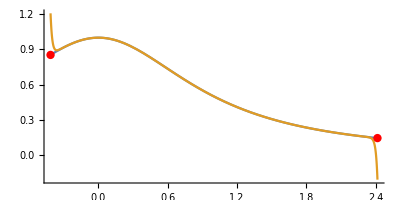

Vediamo in un’ unica tabella tutti i grafici di approssimazione:

```mathematica
(*griglia m x l, con passo p tra i gradi n *)
gr2[f_,xin_,r_,m_,l_,p_]:=GraphicsGrid[Table[Plot[{f,PolTaylor[f,xin,(t+s*l) p+1]}//Evaluate,{x,xin-r,xin+r},PlotRange->{{xin-r,xin+ r},{-1,1}},PlotLabel->"n = "<>ToString[(t+s*l) p+1]],{s,0,m-1},{t,0,l-1}],ImageSizeRaw->Large]
```

Approssimazione del Seno al variare del grado del polinomio:

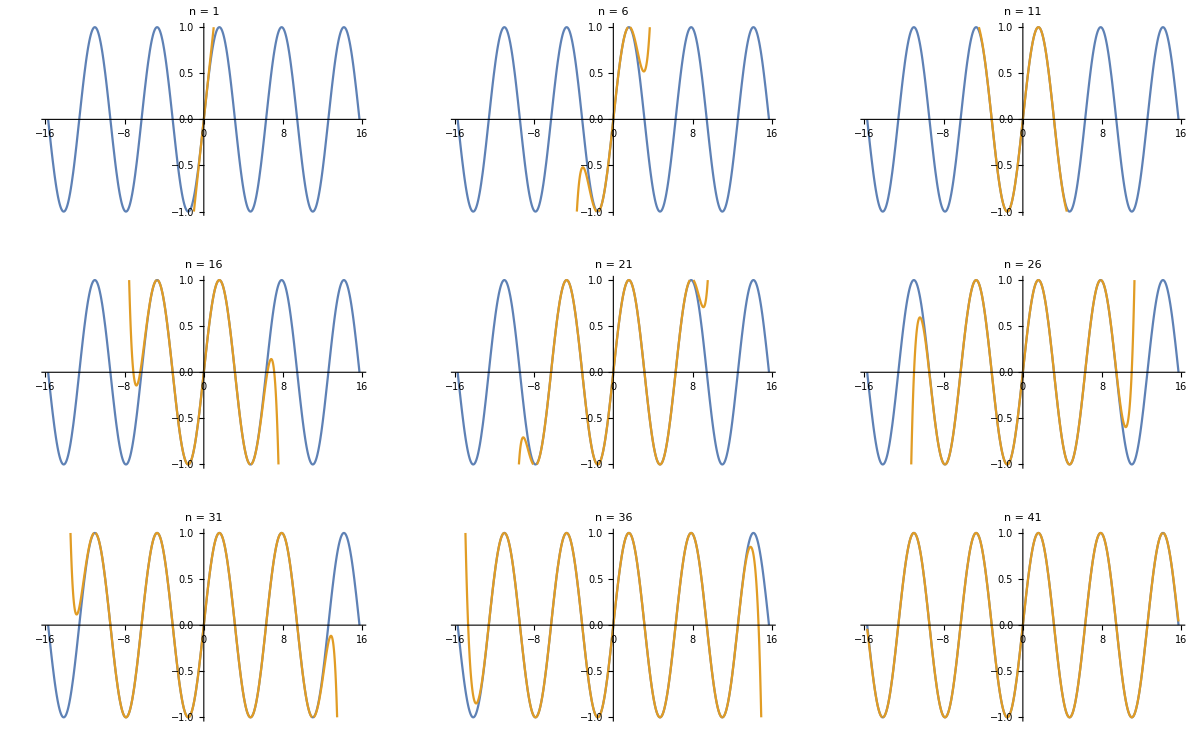

```mathematica
gr2[f[x],0,5Pi,3,3,5]
```

Approssimazione di 1/(1 + x^2) :

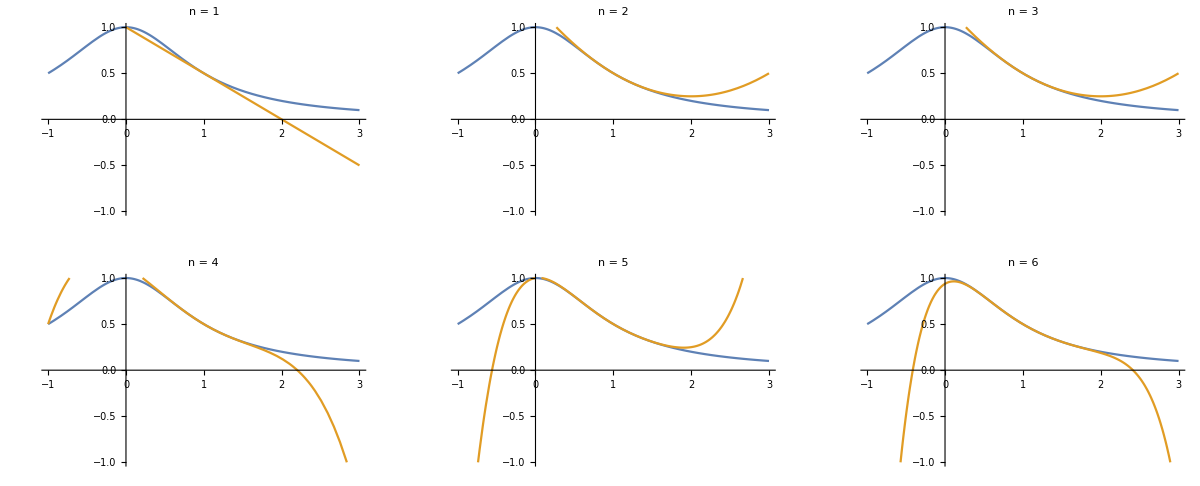

```mathematica
gr2[g[x],1,2,2,3,1]
```

## Esercizio 1.2: Algebra & Coreografie

## Testo dell’esercizio

Le tre radici del polinomio x^3+b x+c dipendono dai coefficienti b e c e sono genericamente complesse (e distinte, ma per speciali valori di b e c una o tutte possono essere reali e due o tutte possono coincidere).
Per ogni scelta di b e c, le radici sono dunque 3 (o 2 o 1) punti nel piano complesso. 
Se si fa muovere il punto (b,c) ϵ ℝ^2 lungo una curva Γ in ℝ^2, le radici si muovono lungo tre curve (che possono avere delle intersezioni) nel piano complesso ℂ.
Si chiede di generare un filmato che mostra, affiancati, il moto del punto (b,c) ϵ ℝ^2 lungo una curva e il corrispondente moto (o “danza”) delle radici in ℂ.

#### Indicazioni

Scegliendo opportunamente la curva Γ nello spazio dei coefficienti si può fare sì che le tre radici “danzino” in modo elegante nel piano complesso.

È opportuno colorare i tre punti in modo diverso.

Volendo potete tracciare anche le traiettorie descritte dai tre punti (come “scie” che si lasciano indietro)

#### Suggerimenti ed osservazioni:

1. Per plottare un numero complesso z nel piano complesso si plottano (Re[z],Im[z]) in  R^2 con ListPlot.

Per plottare più numeri complessi: ListPlot[ { {Re[z_1],Im[z_1]} , {Re[z_2],Im[z_2]} , ....  }

Per plottarli con colori/dimensioni diverse ListPlot[ .....  ,   PlotStyle→{ {direttive x punto 1}, {direttive x punto 2}, ....} ]

2. Scegliere una parametrizzazione
     t→(b[t],c[t])
della curva desiderata. 

Per ogni t, 
    NSolve[ x^3+b[t] x + c[t]==0,x]
produce la lista delle regole di sostituzione alle tre radici. Per plottarle:
    ListPlot[  {{Re[x],Im[x]}} /. ........ ]
Poi
    ListPlot[  {b[t],c[t]} ]
plotta il punto (b,c) nel piano dei coefficienti.

Si possono disporre i due grafici l’uno affianco all’altro con .....

3. Per creare l’animazione si può usare 
         Manipulate[  ......  , {t, .....} ]
oppure
         Animate[  ......  , {t, .....} ] 
Decidete voi (come vi sembra meglio/più bello) se lasciare gli assi etc.
Scegliete la durata dell’animazione come vi sembra meglio.

4. Infine, per creare il filmato (apprezzato, ma non obbligatorio) conviene creare la lista delle immagini “fotogrammi”
       Table[ .....]
e poi esportarla in un opportuno formato grafico.

Attenzione: provate prima creazione ed esportazione con POCHI fotogrammi.    

      Export[  “nome del file” ,  Resolution → ..... , ImageSize → ..... ]
      
Nota: Io non sono un esperto di formati grafici. Mi sembra però che, almeno per immagini semplici come quelle create in questo esercizio, l’Animated GIF sia preferibile all’AVI.

5. Siete liberi di fare diversamente, se vi sembra meglio o prefereribile, e anche di fare più cose (a vostra scelta, purchè pertinenti: cioè, che aiutino o espandano la comprensione dell’esercizio da svolgere).

## Soluzione

Consideriamo un polinomio di 3° grado di questo tipo: x^3 + b x + c    con  b,c in ℝ.
Vogliamo osservare al variare di b,c in ℝ^2, la variazione delle  3  radici complesse.

Innanzitutto scegliamo una prima parametrizzazione della curva. In questo caso abbiamo scelto come curva la Circonferenza. Imponiamo come dominio di definizione [0,2π] . 
La  parametrizzazione della nostra curva è  ℽ : t→ (cos(t),sin(t)).

```mathematica
b[t_]:=Cos[t]
c[t_]:= Sin[t]
```

Adesso, usando ListPlot, disegniamo la curva  (b(t),c(t)) nel piano dei coefficienti e il percorso dei punti di soluzione dell’equazione x^3+b[t] x + c[t]=0. Abbiamo disegnato questi ultimi nel piano complesso, prendendo le loro parti reali e immaginarie.

Per usare  ListPlot dobbiamo prima creare  una lista di punti, una volta che i punti sono stati creati, ListPlot disegna ciascuno di essi nel piano.

1. Per plottare la Circonferenza, usando Table creiamo una lista di punti. All’interno del comando Table, per motivi estetici,  abbiamo usato il comando Hue che rappresenta un colore nello spazio colore HSB con tonalità h (in questo caso con tonalità  t/(2Pi) ).
	
Quindi, usando ListPLot,  per ogni t nell’intervallo  [0, 2π] a passo π/20 (in totale avremo diviso l’intervallo in 40 punti)  disegniamo il punto (cos[t], sin[t]) di dimensione media  e di un colore HSB, secondo lo spazio di colore.

Inoltre, ListPlot ci permette di usare altre opzioni: per esempio, con il comando PlotLabel siamo riusciti a scrivere una legenda, che indica il nome della curva in blu  (abbiamo 	ottenuto questo colore con LabelStyle). In più, abbiamo impostato gli assi neri con AxesStyle.

2.  Adesso disegniamo il percorso dei punti di soluzione dell’equazione, che è un procedimento più complesso.
Prima abbiamo definito la funzione f(t), che rappresenta le soluzioni dell’equazione x^3+b[t] x + c[t]=0. 

Con il comando Map, creiamo una lista di 40 elementi, dove ogni elemento è una lista di 3 elementi: le 3 soluzioni dell’equazione per t = n·(2π)/40, n∈{0, 40}.

 Abbiamo chiamato questa lista di liste “tab1”. Osserviamo che è una lista di 40 elementi. 
 Inoltre, con il comando Range, la variabile t attraversa l’intervallo   [0,2π]   con salto  2π/40 , e  per ogni valore che prende  t = n·(2π)/40,  Map salva nella posizione n (n∈{1, 40})  della lista tab1 le 3 soluzioni dell’equazione per quel valore di t.
 
Una volta che abbiamo ottenuto le soluzioni complesse dell’equazione, e le abbiamo salvate nella lista “tab1”; con il comando {{Re[x],Im[x]}} /. estraiamo la parte reale e immaginaria della soluzione che si trova nella posizione n della lista, creando così la funzione  g(n). Questa funzione, come tab1, crea una lista di liste, cioè una lista di 3 elementi dove ogni elemento è una coordinata nel piano complesso della soluzione dell’elemento n-esimo di tab1. Grazie alla struttura di tab1, con il comando Range[40] possiamo estrarre uno dei 40 elementi che la compongono.

Per ottenere l’insieme di tutti i punti di soluzione, con il comando Flatten possiamo fare un’unica lista di 40·3 punti nel piano complesso, poiché questo comando ci permette di sviluppare la lista fino al primo livello. Sappiamo che per usare il comando Flatten dobbiamo passargli una lista di liste come argomento, in questo caso gli abbiamo passato g[n].
Abbiamo chiamato questo insieme di punti “tab2”. 

Infine disegniamo i punti della lista tab2 con ListPlot, e usiamo gli stessi comandi estetiche che abbiamo usato per disegnare la Circonferenza, e il comando PLotRange che ci permette fissare la lunguezza degli assi.

Siamo riusciti a mettere i grafici  l’uno affianco all’altro con il comando GraphicsRow.

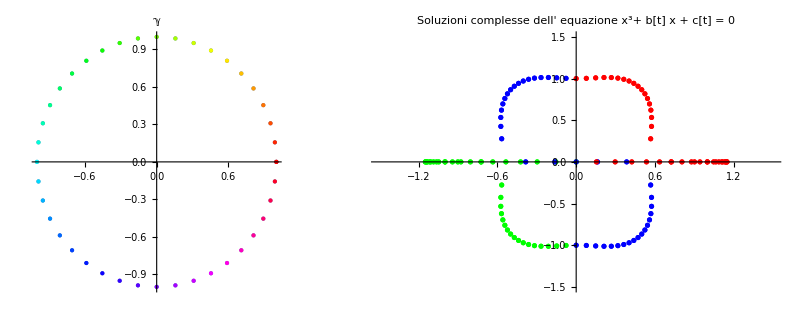

```mathematica
p1=ListPlot[Table[Style[{b[t],c[t]},Hue[t/(2Pi)]],{t,0,2Pi,Pi/20}],PlotStyle->PointSize[Medium], PlotLabel->"ℽ", 
 LabelStyle -> Directive[Blue,12], AxesStyle->Black,AspectRatio->1];

f[t_]:= NSolve[ x^3+b[t] x + c[t]==0,x]
tab1 =Map[f, Range[0,2Pi,Pi/20]];
g[n_]:= {{Re[x],Im[x]}}/. tab1[[n]];
tab2=Flatten[Map[g , Range[40]],1];
p2=ListPlot[tab2, PlotRange -> {{-1.5,1.5},{-1.5,1.5}}, PlotStyle-> {Green,Blue,Red}, PlotLabel->"Soluzioni complesse dell' equazione x^3+ b[t] x + c[t] = 0",LabelStyle -> Directive[Blue,10], AxesStyle->Black];

GraphicsRow[{p1,p2}, ImageSize->Full]
```

Per creare l' animazione usiamo il comando Animate[...]. All’ interno del comando Animate mettiamo il dominio di definizione della curva t →[0, 2π] , la durata della animazione (con  DefaultDuration) e di nuovo il comando ListPlot per disegnare il movimento dei punti appartenenti alla curva e dei punti di soluzione dell’equazione.

Per ottenere i punti di soluzione dell’equazione, prima otteniamo le soluzioni (numeri complessi) dell’equazione con Nsolve, e infine, per ottenere la loro parte reale e immaginaria e poterle così disegnare nel piano complesso, con il comando {{Re[x],Im[x]}}/. sostituiamo la prima coordinata del punto con la parte reale della soluzione e la seconda con la parte immaginaria.


Infine abbiamo fissato l’intervallo degli assi X e Y in modo che non vengano distorti quando i punti si spostano; abbiamo impostato i colori dei punti: verde, blu e rosso; abbiamo aggiunto una legenda con il nome di ogni grafico che abbiamo applicato con il comando LabelStyle in modo che si legga meglio e infine abbiamo messo gli assi neri.

```mathematica
Animate[ListPlot[{{b[t],c[t]}}, PlotRange -> {{-1,1},{-1,1}}, PlotStyle->{Blue, Thick}, PlotLabel->"ℽ", 
 LabelStyle -> Directive[Blue,12], AxesStyle->Black,AspectRatio->1], {t,0,2 Pi}, DefaultDuration->5]

Animate[ListPlot[{{Re[x],Im[x]}}/. NSolve[ x^3+b[t] x + c[t]==0,x], PlotRange -> {{-5,5},{-5,5}}, PlotStyle-> {{Green},{Blue},{Red}}, PlotLabel->"Soluzioni complesse dell' equazione x^3+ b[t] x + c[t] = 0",LabelStyle -> Directive[Blue,10], AxesStyle->Black], {t,0,2 Pi},DefaultDuration->5]
```

Osservazione: I tre punti del piano complesso cambiano colore secondo questo criterio: il colore verde rimane nel terzo quadrante;  quello blu si alterna tra il secondo e il quarto quadrante; e quello rosso rimane nel primo quadrante. 
Questo è dovuto all’ordine lessicografico, che confronta le coordinate delle radici ottenute dall’equazione: assegna il verde a quello con la più piccola coordinata x, il rosso a quello con la più grande coordinata x, e il blu è quello in mezzo.

Infine, per creare il filmato  abbiamo definito la lista delle immagini . Questa lista che abbiamo creato con il comando Table, consiste in una serie di grafici, in particolare 75 grafici, che sono sufficienti affinché l’animazione non vada troppo veloce. Questi 75 grafici sono stati ottenuti dividendo il dominio di definizione della curva [0, 2π] in 75 parti in modo tale che la variabile t abbia un passo di 2π/75 e per ogni t si genera un grafico.

 Ognuno dei grafici è stato creato con il comando ListPlot al quale abbiamo passato gli stessi argomenti della sezione precedente con la differenza che abbiamo ridotto la lunghezza degli assi.

Per concludere l’esercizio abbiamo esportato questa lista di fotogrammi in formato gif. Ho chiamato il file “filmato.gif”. Inoltre il comando Export ci dà la possibilità di definire la risoluzione della nostra gif con Resolution->

```mathematica
fotogrammi1=Table[ListPlot[{{Re[x],Im[x]}}/. NSolve[ x^3+b[t] x + c[t]==0,x],PlotStyle-> {{Green, Thick},{Blue,Thick},{Red, Thick}}, PlotRange -> {{-1.5,1.5},{-1.5,1.5}}],{t, 0, 2 Pi,2 Pi / 75}];
```

```mathematica
Export[  "filmato.gif" , fotogrammi1, Resolution-> 60]
```

filmato.gif

Ora possiamo testare il nostro programma scegliendo un’altra curva, per esempio la Catenaria, che ha un dominio di definizione. (-∞, +∞ ) e parametrizzazione t→(t, a·cosh(t/a)).
Useremo gli stessi comandi che abbiamo usato per la circonferenza, quindi dobbiamo solo cancellare le assegnazioni alle variabili b[t] e c[t] e ripetere la procedura. Impostiamo come dominio di definizione [-10,10] e come variabile a=2.

```mathematica
Clear[b]
Clear[c]
a=2;
b[t_]:=t
c[t_]:= a Cosh[t/a]
```

Disegnamo la Catenaria

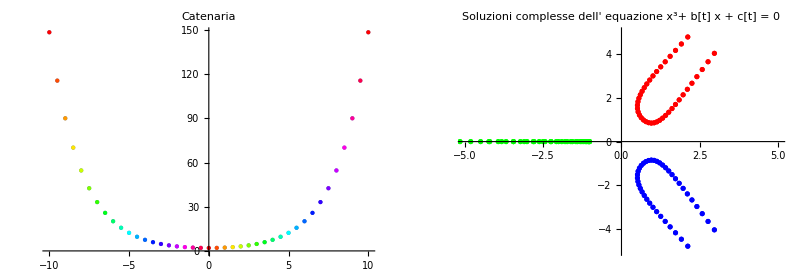

```mathematica
q1:=ListPlot[Table[Style[{b[t],c[t]},Hue[t/10]],{t,-10,10,0.5}],PlotStyle->PointSize[Medium], PlotLabel->"Catenaria", LabelStyle->Directive[Orange,14], AxesStyle->Black];

f[t_]:= NSolve[ x^3+b[t] x + c[t]==0,x]
tab3 =Map[f, Range[-10,10,0.5]];
g[n_]:= {{Re[x],Im[x]}} /. tab3[[n]];
tab4=Flatten[Map[g , Range[40]],1];
q2=ListPlot[tab4, PlotRange -> {{-5,5},{-5,5}}, PlotStyle-> {{Green},{Blue},{Red}}, PlotLabel->"Soluzioni complesse dell' equazione x^3+ b[t] x + c[t] = 0",LabelStyle -> Directive[Blue,10], AxesStyle->Black];

GraphicsRow[{q1,q2}, ImageSize->Full]
```

Facciamo le animazioni della catenaria e delle soluzioni dell’ equazione.

```mathematica
Animate[ListPlot[{{b[t],c[t]}}, PlotRange -> {{-10,10},{0,150}}], {t,-10,10}, DefaultDuration->5]
Animate[ListPlot[{{Re[x],Im[x]}}/. NSolve[ x^3+b[t] x + c[t]==0,x], PlotRange -> {{-5,5},{-5,5}}, PlotStyle-> {{Green},{Blue},{Red}}], {t,-10,10}, DefaultDuration->5]
```

Creamo il fimato

```mathematica
fotogrammi2=Table[ListPlot[{{Re[x],Im[x]}}/. NSolve[ x^3+b[t] x + c[t]==0,x],PlotStyle-> {{Green, Thick},{Blue,Thick},{Red, Thick}}, PlotRange ->{{-5,5},{-5,5}}],{t, -10, 10,0.5}];
Export[  "filmato2.gif" , fotogrammi2,Resolution-> 60]
```

filmato2.gif

## Esercizio 1.3: Teorema dei numeri primi

## Testo dell’esercizio

Il teorema dei numeri primi afferma che le funzioni    π(n)   ,   n/log(n)  ,   li(n)   sono asintotiche per   n→∞ .
Investigare numericamente questa affermazione.

#### Indicazioni :

Produrre dei grafici che mettono in evidenza 

1. se   n/log(n) - π(n)   e   li(n) - π(n)  →  0 per n→∞

2. se   n/log(n),   li(n)  e  π(n)  sono asintotiche per n→∞. 

Se necessario, produrre un’evidenza (utilizzando se opportuno un opportuno grafico log o log-log) del fatto che certe appropriate funzioni → 0

## Soluzione

Il teorema dei numeri primi afferma che le funzioni π(n) (il numro di primi ≤ n), n/log(n), li(n) ( li(n)= (∫_2)^n  ⅆx/(log(x)) ) sono asintotiche per n→∞.
Vogliamo quindi verificare graficamente questo risultato.

```mathematica
Clear[t]
```

Cominciamo con la cancellazione dei valori assegnati alla variabile t e la definizione delle funzioni f e g per le quali vogliamo calcolare i loro limiti quando t tende all’infinito e verificare se tendono a zero.
Poi disegneremo le tre funzioni n/log(n) , π(n)   e   li(n) (lasciamo questa funzione predefinita in Mathematica anche se l’inizio dell’intervallo di integrazione è 0 e non 2 poichè l’andamento della funzione è simile) sullo stesso grafico, e usiamo il comando PlotLegends per identificare ciascuna delle funzioni.

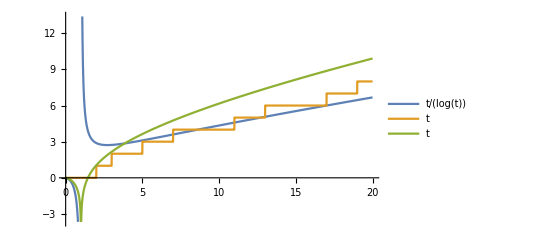

```mathematica
Plot[{t/Log[t], PrimePi[t], LogIntegral[t]}, {t, 0,20}, PlotLegends -> "Expressions"]
```

```mathematica
f[t_]:=t/Log[t]-PrimePi[t]
g[t_]:=LogIntegral[t]-PrimePi[t]
```

Calcoliamo i limiti di f e g usando il comando Limit

```mathematica
Limit[f[t],t->∞]
```

-∞

```mathematica
Limit[g[t],t->Infinity]
```

lim_(t→∞) (LogIntegral[t]-PrimePi[t])

Notiamo che Wolfram Mathematica non è in grado di calcolare il limite quando t tende all’infinito di g[t].
Ma possiamo fare un disegno dei grafici per avere un’idea di dove tendano le funzioni.
In questo caso ho messo la legenda dopo il grafico indicandola con il comando Placed.

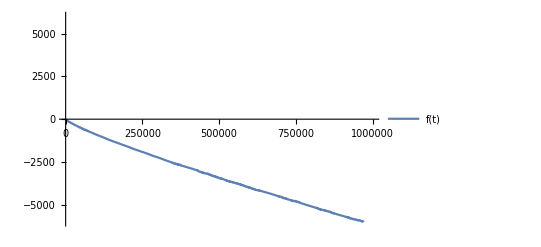

```mathematica
Plot[f[t],{t,0,10^6}, PlotRange-> {-6000,6000}, PlotLegends->Placed[{"f(t)"},After]]
```

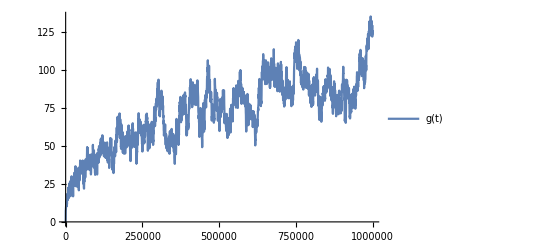

```mathematica
Plot[g[t],{t,0,10^6},PlotLegends->Placed[{"g(t)"},After]]
```

Dai grafici abbiamo trovato che il limite di f(t) è -∞  e il limite di g(t) è +∞ (ma come dal confronto sopra si vede che ci tende molto più lentamente) quindi la funzione π(n) è delimitata superiormente dalla funzione  li(n)  e inferiormente dalla funzione n/log(n) (si vede dal segno sull’asse y della funzione).
Infine, controlliamo che le funzioni siano asintotiche, cioè che il coefficiente di ciascuna di esse tenda a 1.
Per fare ciò, definiamo le funzioni h(t) , i(t) e j(t) che sono i coefficienti delle tre funzioni dell’ enunciato.

```mathematica
h[t_]:=PrimePi[t]/(t/Log[t])
i[t_]:=LogIntegral[t]/PrimePi[t]
j[t_]:=LogIntegral[t]/(t/Log[t])
```

```mathematica
Limit[h[t], t->Infinity]
```

1

```mathematica
Limit[i[t],t->Infinity]
```

1

```mathematica
Limit[j[t],t->Infinity]
```

1

Poiché il limite dei quozienti h e j tende a 1, possiamo essere sicuri che le funzioni π(n) e  n/log(n) così come li(n) e n/log(n) sono asintotiche.
Disegniamo i grafici delle funzioni per conoscere il loro limite quando t tende all’infinito:

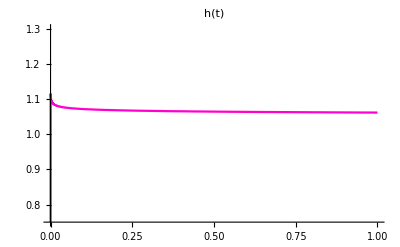

```mathematica
Plot[h[t],{t,0,100000000},PlotRange->{0.75,1.3},PlotLabel->Style["h(t)",Purple,20], ColorFunction-> Hue]
```

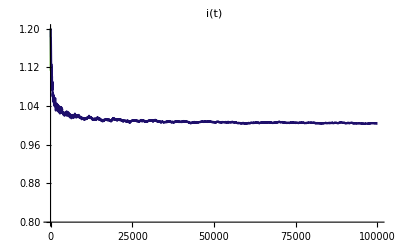

```mathematica
Plot[i[t],{t,0,100000}, PlotRange->{0.8,1.2}, PlotLabel->Style["i(t)",Orange,20],ColorFunction->"BlueGreenYellow"]
```

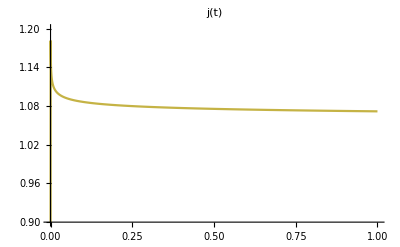

```mathematica
Plot[j[t],{t,0,10000000}, PlotRange->{0.9,1.2},  PlotLabel->Style["j(t)",Red,20],ColorFunction->"Rainbow"]
```

Guardando il grafico non è chiaro se il limite delle funzioni h(t) e j(t) tendono a 1, tuttavia quando si calcola il limite di queste funzioni con il comando Limite, Mathematica ci assicura che entrambi  h(t) e j(t) tendono a 1 molto lentamente.
I limiti delle tre funzioni tendono a uno, quindi π(n), Li(n) e n/logn sono funzioni asintotiche anche se il limite delle differenze delle funzioni f e g, non è 0.

## Esercizio 1.4: Cicloide

## Testo dell’esercizio

Se, nel piano xy, un cerchio di raggio r rotola senza strisciare sull’asse x, un punto P del cerchio descrive, nel piano xy, una curva chiamata cicloide, di equazioni parametriche
   t → (rt - r sin(t) , r - r cos(t) )
Produrre un’animazione (e magari un filmato) che mostra il cerchio (o un disco) che  rotola, il punto P su di essa, e la curva descritta da P nel piano

#### Suggerimenti ed osservazioni:

1. Se il cerchio (o il disco) è graficamente omogeneo, la sua roto-traslazione può essere sostituita dalla sua traslazione e dalla rotazione lungo il suo bordo del punto P. Volendo si può anche far rotolare davvero il cerchio (o il disco)  ma per far apprezzare la rotazione bisogna allora colorarlo o mettere dei raggi come se fosse una ruota, etc.

2. Forse è più bello se la cicloide si “svolge” dietro al punto P, come fosse una scia, ma vedete voi.

## Soluzione

Una cicloide è la curva tracciata sul piano xy da un punto  P0 fissato su una circonferenza che rotola senza strisciare sull’asse x.

Scrivo la parametrizzazione di una cicloide:

```mathematica
Cicloide[r_,tfin_]:=ParametricPlot[{r t-r Sin[t],r -r Cos[t]},{t,0,tfin},AspectRatio->Automatic,PlotRange->{{-r,tfin},{0,2r}},ImageSize->Large]
```

```mathematica
Cicloide[1,4 Pi]
```

Animo ora la rotazione di una circonferenza con punto P0  nell’origine nell’istante iniziale:

definisco gli elementi grafici: il centro della circonferenza, P0, il segmento [P0, centro circonf.], la circonferenza.

```mathematica
Pcentro[t_]:={t,1}
P0[t_,r_]:={r t-r Sin[t],r-r Cos[t]}
P0disco[t_,r_]:={Red,Disk[P0[t,r],0.05]}
sbarra[t_,r_]:={Thickness[0.005],Green,Line[{Pcentro[t],P0[t,r]}]}
ruota[t_,r_]:={Magenta,Circle[Pcentro[t],r]}
```

Creo una funzione che mostra il sistema rotante e la scia della traiettoria svolta fino a quell’istante in un determinato tempo t (come fosse una fotografia del sistema nel dato istante):

```mathematica
gcicl[t_,r_,tfin_]:=Show[Graphics[{sbarra[t,r],ruota[t,r],P0disco[t,r]},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,PlotRange->{{-r,tfin},{0,2r}}],Cicloide[r,t],ImageSize->Large]
```

Definisco una funzione  che anima la funzione “fotogramma” precedente:

```mathematica
moto[tfin_,r_]:=Animate[gcicl[t,r,tfin],{t,0,tfin},AnimationDirection->ForwardBackward]
```

```mathematica
moto[4. Pi,1]
```

## Esercizio 1.5: Gaps fra i primi (facoltativo) (Non c’è obbligo di farlo: farlo solo se si ha piacere di farlo)

## Testo dell’esercizio

Cercare di produrre grafici di π(x),  in diversi intervalli n ≤ x ≤ n+Δn, in modo che si assomiglino.

#### Indicazioni :

Farlo per cinque o sei valori di n compresi fra 10^2 e 10^8 o 10^9.
Scegliere Δn in funzione di n, in modo che il numero k di numeri primi nell’intervallo (n, n+Δn), e dunque il numero di “scalini”, sia (circa) indipendente da n.
Per facilitare il confronto finale, produrre una sola figura con tutti i grafici.

#### Suggerimenti ed osservazioni:

Per scegliere Δn si può procedere in diversi modi, con accuratezza (e lavoro) crescenti:
- per tentativi (giudicando a occhio i grafici ottenuti)
- ricordando il teorema dei numeri primi
- risolvendo un’equazione del tipo
              π(n+h) - π(n) = k 
Siccome π è costante a tratti, questa equazione non si può risolvere con FindRoot. Si può invece risolverla “provando” successivamente tutti i valori di h, fino a che si trova quello giusto. Questo si può fare con una  While[....] (vedere sotto) oppure anche con Do[....,Return[h], ....] (vedere l'Help). Il teorema dei numeri primi permette di velocizzare questa operazione?

◼ While[test, body] evaluates test, then body, repetitively, until test first fails to give True.

Esempio: per definire in modo random un numero intero DISPARI:

```mathematica
x=0;
While[ EvenQ[x], x=Random[Integer,{0,100}] ];
x
Clear[x]
```

89

## Soluzione

Vogliamo mostrare se in intervalli diversi la funzione π(n) ha un andamento simile.
Innanzitutto creiamo  5 valori diversi di n e chiamamoli nk con k∈{1,...,6}:

```mathematica
n1=150;
n2=10^3;
n3=1.2*10^4;
n4=10^5;
n5=3*10^7;
n6=7*10^7;
```

Adesso, fissiamo k (n° di numeri primi che sarà presente nell’intervallo), che non va in funzione di n, e cerchiamo di trovare l’incremento Δn (intervallo in cui per ogni n fissato si hanno k numeri primi) in funzione di  n.

```mathematica
k=25;
```

Adesso calcoliamo π(nk)  per  k={1,.....,5}  (è la funzione PrimePi ) e cerchiamo dni (la lunghezza dell’intevallo in funzione di nk in cui la funzione ha k numeri primi a partire da ni) .
Osservazione: da quanto visto nell’esercizio 3 che π(n) ≥ n/log(n) almeno da un certo n in poi (dedotto dai grafici prodotti). 
Per diminuire la complessità computazionale di While, nel cercare dnk in funzione di n, scelgo il valore da cui partire la valutazione del probabile dni  dalla soluzione dell’equazione: n/log(n)=k.
In questo modo evito il controllo di valori che sicuramente risulteranno non idonei.
Poi faccio valutare questo probabile valore iniziale a While, che in caso in tale intervallo vi siano meno di k primi incrementa di 2 il valore di  dni e continua la ricerca, altimenti ne assegna definitivamente il valore.

```mathematica
pn1 = PrimePi[n1];
dn1=x/.FindRoot[x/Log[x]==k + pn1,{x,1.01(*metto questo punto di inizializzazione poichè le funzioni π(n) e x/Log[x] differiscono vicino all'origine*)}];
While[PrimePi[n1+dn1]-pn1<k, dn1=dn1+2];
dn1

pn2= PrimePi[n2];
dn2=x/.FindRoot[x/Log[x]==k + pn2,{x,1.01}];
While[PrimePi[n2+dn2]-pn2<k, dn2=dn2+2];
dn2

pn3= PrimePi[n3];
dn3=x/.FindRoot[x/Log[x]==k + pn3,{x,1.01}];
While[PrimePi[n3+dn3]-pn3<k, dn3=dn3+2];
dn3

pn4= PrimePi[n4];
dn4=x/.FindRoot[x/Log[x]==k + pn4,{x,1.01}];
While[PrimePi[n4+dn4]-pn4<k, dn4=dn4+2];
dn4

pn5= PrimePi[n5];
dn5=x/.FindRoot[x/Log[x]==k + pn5,{x,1.01}];
While[PrimePi[n5+dn5]-pn5<k, dn5=dn5+2];
dn5

dn6 = 2*k;
pn6 = PrimePi[n6];
While[PrimePi[n6+dn6]-pn6<k, dn6=dn6+2];
dn6
```

Oppure
sappiamo che l’ incremento comicia almeno in 2*k perché k è il numero di primi tra π(n1) e π(n1+dn1)
Facciamo questo per fare meno operazioni nel While eseguendo questa serie di comandi:

dn1 = 2*k;
pn1 = PrimePi[n1];
While[PrimePi[n1 + dn1] - pn1 < k, dn1 = dn1 + 2];
dn1

dn2 = 2*k;
pn2 = PrimePi[n2];
While[PrimePi[n2 + dn2] - pn2 < k, dn2 = dn2 + 2];
dn2

dn3 = 2*k;
pn3 = PrimePi[n3];
While[PrimePi[n3 + dn3] - pn3 < k, dn3 = dn3 + 2];
dn3

dn4 = 2*k;
pn4 = PrimePi[n4];
While[PrimePi[n4 + dn4] - pn4 < k, dn4 = dn4 + 2];
dn4

dn5 = 2*k;
pn5 = PrimePi[n5];
While[PrimePi[n5 + dn5] - pn5 < k, dn5 = dn5 + 2];
dn5

dn6 = 2*k;
pn6 = PrimePi[n6];
While[PrimePi[n6 + dn6] - pn6 < k, dn6 = dn6 + 2];
dn6

Cerco dni più piccolo poichè voglio poi sovrapporre i grafici oppurtunamente riscalati:

```mathematica
min=Min[{dn1,dn2,dn3,dn4,dn5,dn6}]
```

Adesso mostriamo i grafici in queste regioni:

Definisco la funzione f che mostra il variare di numero di primi nell’ intervallo [ ni, dni ] con l’asse x opportunamente riscalato in modo tale da poter sovrappore tutti i grafici nell’intervallo di esistenza minore: per t ∈ [0,min].
Non potrei altrimenti sovvraporre i grafici in modo significativo, ciò che si vuole far notare è infatti la distribuzione di primi all’interno dell’intervallo.

```mathematica
f[ni_,dni_]:=PrimePi[ni+dni/min t]-PrimePi[ni]
```

Plottiamo in un unico grafico tutte le funzioni:

Nella legenda vediamo l’intervallo di distribuzione di primi

```mathematica
Plot[{f[n1,dn1],f[n2,dn2],f[n3,dn3],f[n4,dn4],f[n5,dn5],f[n6,dn6]},{t,0,min},PlotStyle->{Blue,Red,Magenta,Green,Gray,Orange},Ticks->False,ImageSize->Large,PlotLegends->Placed[{"["<>ToString[n1]<>", "<>ToString[n1+dn1]<>"]","["<>ToString[n2]<>", "<>ToString[n2+dn2]<>"]","["<>ToString[n3]<>", "<>ToString[n3+dn3]<>"]","["<>ToString[n4]<>", "<>ToString[n4+dn4]<>"]","["<>ToString[n5]<>", "<>ToString[n5+dn5]<>"]","["<>ToString[n6]<>", "<>ToString[n6+dn6]<>"]"},After],PlotLabel->"π(n)"]
```

Possiamo notare un andamento simile nella distribuzione di primi al’interno dell’intervallo